## Las funciones de los armónicos esféricos vectoriales figuran a continuación

```mathematica
Off[NIntegrate::izero];Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];Off[NIntegrate::eincr];Off[NIntegrate::ncvi]
```

### Definiciones

```mathematica
LegendrePDer0[n_,m_,theta_]:=-(1+n) Cot[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) Csc[theta] LegendreP[1+n,m,Cos[theta]]
```

```mathematica
LegendrePDer1[n_,m_,theta_]:=-If[m==0,LegendreP[n,1,Cos[theta]],If[m>0,1/2((n-m+1)(n+m) LegendreP[n,m-1,Cos[theta]]-LegendreP[n,m+1,Cos[theta]]),(-1)^m (n+m)!/(n-m)!  1/2((n+m+1)(n-m) LegendreP[n,-m-1,Cos[theta]]-LegendreP[n,-m+1,Cos[theta]])]]
```

```mathematica
LegendrePDer[n_,m_,theta_]:=-1/2 ((n+m)(n-m+1) LegendreP[n,m-1,Cos[theta]]-LegendreP[n,m+1,Cos[theta]])
```

#### Comprobación

```mathematica
Flatten[With[{theta=10. Degree},Table[{n,m,LegendrePDer0[n,m,theta],LegendrePDer1[n,m,theta],LegendrePDer[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

(1 | -1 | 0.492404 | 0.492404 | 0.492404
1 | 0 | -0.173648 | 0.173648 | -0.173648
1 | 1 | -0.984808 | -0.984808 | -0.984808
2 | -2 | 0.0427525 | 0.0427525 | 0.0427525
2 | -1 | 0.469846 | 0.469846 | 0.469846
2 | 0 | -0.51303 | 0.51303 | -0.51303
2 | 1 | -2.81908 | -2.81908 | -2.81908
2 | 2 | 1.02606 | 1.02606 | 1.02606
3 | -3 | 0.00185597 | 0.00185597 | 0.00185597
3 | -2 | 0.0414485 | 0.0414485 | 0.0414485
3 | -1 | 0.436725 | 0.436725 | 0.436725
3 | 0 | -1.00262 | 1.00262 | -1.00262
3 | 1 | -5.2407 | -5.2407 | -5.2407
3 | 2 | 4.97382 | 4.97382 | 4.97382
3 | 3 | -1.3363 | -1.3363 | -1.3363
4 | -4 | 0.0000537144 | 0.0000537144 | 0.0000537144
4 | -3 | 0.00180884 | 0.00180884 | 0.00180884
4 | -2 | 0.0397445 | 0.0397445 | 0.0397445
4 | -1 | 0.393875 | 0.393875 | 0.393875
4 | 0 | -1.61986 | 1.61986 | -1.61986
4 | 1 | -7.8775 | -7.8775 | -7.8775
4 | 2 | 14.308 | 14.308 | 14.308
4 | 3 | -9.11653 | -9.11653 | -9.11653
4 | 4 | 2.16577 | 2.16577 | 2.16577
5 | -5 | 1.16593×10^-6 | 1.16593×10^-6 | 1.16593×10^-6
5 | -4 | 0.0000524872 | 0.0000524872 | 0.0000524872
5 | -3 | 0.00175104 | 0.00175104 | 0.00175104
5 | -2 | 0.0376694 | 0.0376694 | 0.0376694
5 | -1 | 0.342378 | 0.342378 | 0.342378
5 | 0 | -2.33604 | 2.33604 | -2.33604
5 | 1 | -10.2713 | -10.2713 | -10.2713
5 | 2 | 31.6423 | 31.6423 | 31.6423
5 | 3 | -35.301 | -35.301 | -35.301
5 | 4 | 19.0466 | 19.0466 | 19.0466
5 | 5 | -4.23091 | -4.23091 | -4.23091)

```mathematica
Flatten[With[{theta=0 Degree},Table[{n,m,LegendrePDer0[n,m,theta],LegendrePDer1[n,m,theta],LegendrePDer[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

(1 | -1 | Indeterminate | 1/2 | 1/2
1 | 0 | Indeterminate | 0 | 0
1 | 1 | Indeterminate | -1 | -1
2 | -2 | Indeterminate | 0 | 0
2 | -1 | Indeterminate | 1/2 | 1/2
2 | 0 | Indeterminate | 0 | 0
2 | 1 | Indeterminate | -3 | -3
2 | 2 | Indeterminate | 0 | 0
3 | -3 | Indeterminate | 0 | 0
3 | -2 | Indeterminate | 0 | 0
3 | -1 | Indeterminate | 1/2 | 1/2
3 | 0 | Indeterminate | 0 | 0
3 | 1 | Indeterminate | -6 | -6
3 | 2 | Indeterminate | 0 | 0
3 | 3 | Indeterminate | 0 | 0
4 | -4 | Indeterminate | 0 | 0
4 | -3 | Indeterminate | 0 | 0
4 | -2 | Indeterminate | 0 | 0
4 | -1 | Indeterminate | 1/2 | 1/2
4 | 0 | Indeterminate | 0 | 0
4 | 1 | Indeterminate | -10 | -10
4 | 2 | Indeterminate | 0 | 0
4 | 3 | Indeterminate | 0 | 0
4 | 4 | Indeterminate | 0 | 0
5 | -5 | Indeterminate | 0 | 0
5 | -4 | Indeterminate | 0 | 0
5 | -3 | Indeterminate | 0 | 0
5 | -2 | Indeterminate | 0 | 0
5 | -1 | Indeterminate | 1/2 | 1/2
5 | 0 | Indeterminate | 0 | 0
5 | 1 | Indeterminate | -15 | -15
5 | 2 | Indeterminate | 0 | 0
5 | 3 | Indeterminate | 0 | 0
5 | 4 | Indeterminate | 0 | 0
5 | 5 | Indeterminate | 0 | 0)

### Más definiciones

```mathematica
LegendrePDerSin0[n_,m_,theta_]:=-(1+n) Cos[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) LegendreP[1+n,m,Cos[theta]]
```

```mathematica
LegendrePDerSin[n_,m_,theta_]:=Sin[theta] LegendrePDer[n,m,theta]
```

#### Comprobación (II)

```mathematica
Flatten[With[{theta=10. Degree},Table[{n,m,LegendrePDerSin0[n,m,theta],LegendrePDerSin[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

(1 | -1 | 0.085505 | 0.085505
1 | 0 | -0.0301537 | -0.0301537
1 | 1 | -0.17101 | -0.17101
2 | -2 | 0.0074239 | 0.0074239
2 | -1 | 0.081588 | 0.081588
2 | 0 | -0.0890868 | -0.0890868
2 | 1 | -0.489528 | -0.489528
2 | 2 | 0.178174 | 0.178174
3 | -3 | 0.000322287 | 0.000322287
3 | -2 | 0.00719746 | 0.00719746
3 | -1 | 0.0758364 | 0.0758364
3 | 0 | -0.174103 | -0.174103
3 | 1 | -0.910037 | -0.910037
3 | 2 | 0.863695 | 0.863695
3 | 3 | -0.232046 | -0.232046
4 | -4 | 9.32741×10^-6 | 9.32741×10^-6
4 | -3 | 0.000314101 | 0.000314101
4 | -2 | 0.00690156 | 0.00690156
4 | -1 | 0.0683957 | 0.0683957
4 | 0 | -0.281286 | -0.281286
4 | 1 | -1.36791 | -1.36791
4 | 2 | 2.48456 | 2.48456
4 | 3 | -1.58307 | -1.58307
4 | 4 | 0.376081 | 0.376081
5 | -5 | 2.02461×10^-7 | 2.02461×10^-7
5 | -4 | 9.11431×10^-6 | 9.11431×10^-6
5 | -3 | 0.000304065 | 0.000304065
5 | -2 | 0.00654123 | 0.00654123
5 | -1 | 0.0594534 | 0.0594534
5 | 0 | -0.40565 | -0.40565
5 | 1 | -1.7836 | -1.7836
5 | 2 | 5.49463 | 5.49463
5 | 3 | -6.12995 | -6.12995
5 | 4 | 3.3074 | 3.3074
5 | 5 | -0.73469 | -0.73469)

```mathematica
Flatten[With[{theta=0 Degree},Table[{n,m,LegendrePDerSin0[n,m,theta],LegendrePDerSin[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

(1 | -1 | 0 | 0
1 | 0 | 0 | 0
1 | 1 | 0 | 0
2 | -2 | 0 | 0
2 | -1 | 0 | 0
2 | 0 | 0 | 0
2 | 1 | 0 | 0
2 | 2 | 0 | 0
3 | -3 | 0 | 0
3 | -2 | 0 | 0
3 | -1 | 0 | 0
3 | 0 | 0 | 0
3 | 1 | 0 | 0
3 | 2 | 0 | 0
3 | 3 | 0 | 0
4 | -4 | 0 | 0
4 | -3 | 0 | 0
4 | -2 | 0 | 0
4 | -1 | 0 | 0
4 | 0 | 0 | 0
4 | 1 | 0 | 0
4 | 2 | 0 | 0
4 | 3 | 0 | 0
4 | 4 | 0 | 0
5 | -5 | 0 | 0
5 | -4 | 0 | 0
5 | -3 | 0 | 0
5 | -2 | 0 | 0
5 | -1 | 0 | 0
5 | 0 | 0 | 0
5 | 1 | 0 | 0
5 | 2 | 0 | 0
5 | 3 | 0 | 0
5 | 4 | 0 | 0
5 | 5 | 0 | 0)

### Más definiciones

```mathematica
mLegendrePDividedBySin0[n_,m_,theta_]:=m LegendreP[n,m,Cos[theta]]/Sin[theta]
```

```mathematica
mLegendrePDividedBySin1[n_,m_,theta_]:=If[m==0,0,If[m>0,1/2 Cos[theta]((n-m+1)(n+m) LegendreP[n,m-1,Cos[theta]]+LegendreP[n,m+1,Cos[theta]])+m Sin[theta] LegendreP[n,m,Cos[theta]],(-1)^m (n+m)!/(n-m)!  1/2 Cos[theta]((n+m+1)(n-m) LegendreP[n,-m-1,Cos[theta]]+LegendreP[n,-m+1,Cos[theta]])-m Sin[theta] LegendreP[n,-m,Cos[theta]]]]
```

```mathematica
mLegendrePDividedBySin[n_,m_,theta_]:=-1/2(LegendreP[n-1,m+1,Cos[theta]]+(n+m-1)(n+m) LegendreP[n-1,m-1,Cos[theta]])
```

#### Comprobación (III)

```mathematica
Flatten[With[{theta=10. Degree},Table[{n,m,mLegendrePDividedBySin0[n,m,theta],mLegendrePDividedBySin1[n,m,theta],mLegendrePDividedBySin[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

(1 | -1 | -0.5 | -0.515077 | -0.5
1 | 0 | 0. | 0 | 0.
1 | 1 | -1. | 0.939693 | -1.
2 | -2 | -0.043412 | -0.0106862 | -0.043412
2 | -1 | -0.492404 | -0.566643 | -0.492404
2 | 0 | 0. | 0 | 0.
2 | 1 | -2.95442 | 2.77625 | -2.95442
2 | 2 | 1.04189 | -0.979055 | 1.04189
3 | -3 | -0.00188461 | -0.0427438 | -0.00188461
3 | -2 | -0.0427525 | 0.113234 | -0.0427525
3 | -1 | -0.481154 | -0.640748 | -0.481154
3 | 0 | 0. | 0 | 0.
3 | 1 | -5.77385 | 5.42564 | -5.77385
3 | 2 | 5.1303 | -4.82091 | 5.1303
3 | 3 | -1.35692 | 1.27508 | -1.35692
4 | -4 | -0.0000545431 | 0.0662604 | -0.0000545431
4 | -3 | -0.00185597 | -0.283861 | -0.00185597
4 | -2 | -0.0418848 | 0.414052 | -0.0418848
4 | -1 | -0.46642 | -0.733642 | -0.46642
4 | 0 | 0. | 0 | 0.
4 | 1 | -9.3284 | 8.76583 | -9.3284
4 | 2 | 15.0785 | -14.1692 | 15.0785
4 | 3 | -9.35411 | 8.78999 | -9.35411
4 | 4 | 2.19918 | -2.06655 | 2.19918
5 | -5 | -1.18391×10^-6 | -0.129547 | -1.18391×10^-6
5 | -4 | -0.0000537144 | 0.5877 | -0.0000537144
5 | -3 | -0.00182067 | -1.10855 | -0.00182067
5 | -2 | -0.0408188 | 0.994315 | -0.0408188
5 | -1 | -0.448424 | -0.840552 | -0.448424
5 | 0 | 0. | 0 | 0.
5 | 1 | -13.4527 | 12.6414 | -13.4527
5 | 2 | 34.2878 | -32.22 | 34.2878
5 | 3 | -36.7048 | 34.4912 | -36.7048
5 | 4 | 19.4919 | -18.3164 | 19.4919
5 | 5 | -4.29618 | 4.03709 | -4.29618)

```mathematica
Flatten[With[{theta=0 Degree},Table[{n,m,mLegendrePDividedBySin0[n,m,theta],mLegendrePDividedBySin[n,m,theta]},{n,1,5},{m,-n,n}]],1]//MatrixForm
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

(1 | -1 | Indeterminate | -1/2
1 | 0 | Indeterminate | 0
1 | 1 | Indeterminate | -1
2 | -2 | Indeterminate | 0
2 | -1 | Indeterminate | -1/2
2 | 0 | Indeterminate | 0
2 | 1 | Indeterminate | -3
2 | 2 | Indeterminate | 0
3 | -3 | Indeterminate | 0
3 | -2 | Indeterminate | 0
3 | -1 | Indeterminate | -1/2
3 | 0 | Indeterminate | 0
3 | 1 | Indeterminate | -6
3 | 2 | Indeterminate | 0
3 | 3 | Indeterminate | 0
4 | -4 | Indeterminate | 0
4 | -3 | Indeterminate | 0
4 | -2 | Indeterminate | 0
4 | -1 | Indeterminate | -1/2
4 | 0 | Indeterminate | 0
4 | 1 | Indeterminate | -10
4 | 2 | Indeterminate | 0
4 | 3 | Indeterminate | 0
4 | 4 | Indeterminate | 0
5 | -5 | Indeterminate | 0
5 | -4 | Indeterminate | 0
5 | -3 | Indeterminate | 0
5 | -2 | Indeterminate | 0
5 | -1 | Indeterminate | -1/2
5 | 0 | Indeterminate | 0
5 | 1 | Indeterminate | -15
5 | 2 | Indeterminate | 0
5 | 3 | Indeterminate | 0
5 | 4 | Indeterminate | 0
5 | 5 | Indeterminate | 0)

#### Más definiciones

```mathematica
(*hRDer[n_,k_,R_]:=((1+n) SphericalHankelH1[n,k R])/(k R)-SphericalHankelH1[1+n,k R]*)
```

```mathematica
hRDer[n_,k_,R_]:=(1+n) SphericalHankelH1[n,k R]-k R SphericalHankelH1[1+n,k R]
```

```mathematica
gamma[m_,n_]:=Sqrt[(2 n+1)(n-m)!/(4 Pi n(n+1)(n+m)!)]
```

```mathematica
Pfunc[m_,n_,theta_,phi_]:={LegendreP[n,m,Cos[theta]] Exp[I m phi],0,0}
```

```mathematica
BSinfunc[m_,n_,theta_,phi_]:={0,LegendrePDerSin[n,m,theta],I m LegendreP[n,m,Cos[theta]]} Exp[I m phi]
```

```mathematica
CSinfunc[m_,n_,theta_,phi_]:={0,I m LegendreP[n,m,Cos[theta]],-LegendrePDerSin[n,m,theta]} Exp[I m phi]
```

```mathematica
MSinfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n] SphericalHankelH1[n,k R] CSinfunc[m,n,theta,phi]
```

```mathematica
(*NSinfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n] hRDer[n,k,R] Cfunc[m,n,theta,phi]*)
```

```mathematica
NSinfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n](n(n+1) SphericalHankelH1[n,k R]/(k R) Pfunc[m,n,theta,phi] Sin[theta]+ hRDer[n,k,R]/(k R) BSinfunc[m,n,theta,phi])
```

```mathematica
Bfunc[m_,n_,theta_,phi_]:={0,LegendrePDer[n,m,theta],I mLegendrePDividedBySin[n,m,theta]} Exp[I m phi]
```

```mathematica
Cfunc[m_,n_,theta_,phi_]:={0,I mLegendrePDividedBySin[n,m,theta],-LegendrePDer[n,m,theta]} Exp[I m phi]
```

```mathematica
Mfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n] SphericalHankelH1[n,k R] Cfunc[m,n,theta,phi]
```

```mathematica
(*NSinfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n] hRDer[n,k,R] Cfunc[m,n,theta,phi]*)
```

```mathematica
Nfunc[m_,n_,k_,R_,theta_,phi_]:=gamma[m,n](n(n+1) SphericalHankelH1[n,k R]/(k R) Pfunc[m,n,theta,phi] + hRDer[n,k,R]/(k R) Bfunc[m,n,theta,phi])
```

```mathematica
z1[m_,n_]:=(-1)^m 4 Pi/(2 n+1)
```

```mathematica
z2[m_,n_]:=(-1)^m 4 Pi n(n+1)/(2 n+1)
```

```mathematica
z3[m_,n_]:=(-1)^m 4 Pi n(n+1)/(2 n+1)
```

```mathematica
afunc[gdata_,m_,n_,k_,R_]:=(-1)^m/(4 Pi gamma[m,n]) gdata[[n]][[n+m+1]]1/SphericalHankelH1[n,k R]
```

```mathematica
bfunc[edata_,m_,n_,k_,R_]:=(-1)^m/(4 Pi gamma[m,n]) edata[[n]][[n+m+1]]k R/hRDer[n,k,R]
```

```mathematica
b2func[ddata_,m_,n_,k_,R_]:=(-1)^m/(4 Pi gamma[m,n]) ddata[[n]][[n+m+1]] k R/SphericalHankelH1[n,k R]
```

```mathematica
EfieldTerms[k_,R_,theta_,phi_,edata_,gdata_,M_]:=Table[(2 n+1)/(n(n+1))(afunc[gdata,m,n,k,R] Mfunc[m,n,k,R,theta,phi]+bfunc[edata,m,n,k,R] Nfunc[m,n,k,R,theta,phi]),{n,1,M},{m,-n,n}]
```

```mathematica
Efieldsint[k_,R_,acoeff_,bcoeff_,theta_,phi_,M_]:=Sum[(2 n+1)/(n(n+1))(acoeff[[n]][[m+n+1]] Mfunc[m,n,k,R,theta,phi]+bcoeff[[n]][[m+n+1]] Nfunc[m,n,k,R,theta,phi]),{n,1,M},{m,-n,n}]
```

```mathematica
Efield[k_,R_,theta_,phi_,edata_,gdata_,M_]:=Sum[(2 n+1)/(n(n+1))(afunc[gdata,m,n,k,R] Mfunc[m,n,k,R,theta,phi]+bfunc[edata,m,n,k,R] Nfunc[m,n,k,R,theta,phi]),{n,1,M},{m,-n,n}]
```

```mathematica
With[{lambda=1.},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,theta=0,phi=0,numberOfModes=1},EfieldTerms[k,r,theta,phi,edata,gdata,numberOfModes]]]
```

{{{0.+0. ⅈ,-1.21127×10^-16-7.65725×10^-17 ⅈ,-7.65725×10^-17+1.21127×10^-16 ⅈ},{-1.19842+0.200655 ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,-1.04853×10^-16+1.74795×10^-16 ⅈ,1.74795×10^-16+1.04853×10^-16 ⅈ}}}

```mathematica
With[{lambda=1.},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,theta=0 Degree,phi=0,numberOfModes=2},Efield[k,r,theta,phi,edata,gdata,numberOfModes]]]
```

{-1.19842+0.200655 ⅈ,-3.79534×10^-16+5.59795×10^-16 ⅈ,5.59795×10^-16+3.79534×10^-16 ⅈ}

#### Simplificaciones

```mathematica
FullSimplify[D[LegendreP[n,m,Cos[theta]],{theta,1}]]
```

-(1+n) Cot[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) Csc[theta] LegendreP[1+n,m,Cos[theta]]

```mathematica
FullSimplify[Sin[theta] D[LegendreP[n,m,Cos[theta]],{theta,1}]]
```

-(1+n) Cos[theta] LegendreP[n,m,Cos[theta]]+(1-m+n) LegendreP[1+n,m,Cos[theta]]

```mathematica
FullSimplify[D[z SphericalHankelH1[n,z],{z,1}]]/.{z->k R}
```

(1+n) SphericalHankelH1[n,k R]-k R SphericalHankelH1[1+n,k R]

```mathematica
FullSimplify[D[z SphericalHankelH1[n,z],{z,1}]/z]/.{z->k R}
```

```mathematica
((1+n) SphericalHankelH1[n,k R])/(k R)-SphericalHankelH1[1+n,k R]
```

```mathematica
Series[-SphericalHankelH1[1,k R],{R,0,2}]
```

(-1)^Floor[(π-Arg[k]-Arg[R])/(2 π)] (ⅈ/(k^2 R^2)+ⅈ/2-(k R)/3-1/8 ⅈ k^2 R^2+O[R]^3)

#### Ortogonalidad

```mathematica
Table[{m,n},{n,0,1},{m,-n,n}]
```

{{{0,0}},{{-1,1},{0,1},{1,1}}}

```mathematica
Table[NIntegrate[Pfunc[m,n,theta,phi].Pfunc[-m,n,theta,phi] Sin[theta],{theta,0,Pi},{phi,0,2 Pi}],{n,0,5},{m,-n,n}]//MatrixForm
```

({12.5664}
{-4.18879,4.18879,-4.18879}
{2.51327,-2.51327,2.51327,-2.51327,2.51327}
{-1.7952,1.7952,-1.7952,1.7952,-1.7952,1.7952,-1.7952}
{1.39626,-1.39626,1.39626,-1.39626,1.39626,-1.39626,1.39626,-1.39626,1.39626}
{-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424})

```mathematica
Table[z1[m,n],{n,0,5},{m,-n,n}]//MatrixForm//N
```

({12.5664}
{-4.18879,4.18879,-4.18879}
{2.51327,-2.51327,2.51327,-2.51327,2.51327}
{-1.7952,1.7952,-1.7952,1.7952,-1.7952,1.7952,-1.7952}
{1.39626,-1.39626,1.39626,-1.39626,1.39626,-1.39626,1.39626,-1.39626,1.39626}
{-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424,1.1424,-1.1424})

```mathematica
Chop[Table[NIntegrate[Pfunc[m,n,theta,phi].BSinfunc[-m,n,theta,phi] ,{theta,0,Pi},{phi,0,2 Pi},Method->"MultiDimensionalRule"],{n,0,5},{m,-n,n}]]//MatrixForm
```

({0}
{0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0})

```mathematica
Chop[Table[NIntegrate[Pfunc[m,n,theta,phi].CSinfunc[-m,n,theta,phi] ,{theta,0,Pi},{phi,0,2 Pi},Method->"MultiDimensionalRule"],{n,0,5},{m,-n,n}]]//MatrixForm
```

({0}
{0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0})

```mathematica
Table[NIntegrate[BSinfunc[m,n,theta,phi].BSinfunc[-m,n,theta,phi]/Sin[theta],{theta,0,Pi},{phi,0,2 Pi}],{n,0,5},{m,-n,n}]//MatrixForm
```

({0.}
{-8.37758,8.37758,-8.37758}
{15.0796,-15.0796,15.0796,-15.0796,15.0796}
{-21.5423,21.5423,-21.5423,21.5423,-21.5423,21.5423,-21.5423}
{27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253}
{-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719})

```mathematica
Table[z2[m,n],{n,0,5},{m,-n,n}]//MatrixForm//N
```

({0.}
{-8.37758,8.37758,-8.37758}
{15.0796,-15.0796,15.0796,-15.0796,15.0796}
{-21.5423,21.5423,-21.5423,21.5423,-21.5423,21.5423,-21.5423}
{27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253}
{-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719})

```mathematica
Chop[Table[NIntegrate[BSinfunc[m,n,theta,phi].CSinfunc[-m,n,theta,phi]/Sin[theta],{theta,0,Pi},{phi,0,2 Pi}],{n,0,5},{m,-n,n}]]//MatrixForm
```

({0}
{0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0})

```mathematica
Chop[Table[NIntegrate[CSinfunc[m,n,theta,phi].CSinfunc[-m,n,theta,phi]/Sin[theta],{theta,0,Pi},{phi,0,2 Pi}],{n,0,5},{m,-n,n}]]//MatrixForm
```

({0}
{-8.37758,8.37758,-8.37758}
{15.0796,-15.0796,15.0796,-15.0796,15.0796}
{-21.5423,21.5423,-21.5423,21.5423,-21.5423,21.5423,-21.5423}
{27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253}
{-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719})

```mathematica
Table[z3[m,n],{n,0,5},{m,-n,n}]//MatrixForm//N
```

({0.}
{-8.37758,8.37758,-8.37758}
{15.0796,-15.0796,15.0796,-15.0796,15.0796}
{-21.5423,21.5423,-21.5423,21.5423,-21.5423,21.5423,-21.5423}
{27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253,-27.9253,27.9253}
{-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719,34.2719,-34.2719})

## Campo Sintetizado

```mathematica
acoeff=With[{numberOfModes=5},Table[(1/n)^Abs[m],{n,1,numberOfModes},{m,-n,n}]]
```

{{1,1,1},{1/4,1/2,1,1/2,1/4},{1/27,1/9,1/3,1,1/3,1/9,1/27},{1/256,1/64,1/16,1/4,1,1/4,1/16,1/64,1/256},{1/3125,1/625,1/125,1/25,1/5,1,1/5,1/25,1/125,1/625,1/3125}}

```mathematica
acoeff//MatrixForm
```

({1,1,1}
{1/4,1/2,1,1/2,1/4}
{1/27,1/9,1/3,1,1/3,1/9,1/27}
{1/256,1/64,1/16,1/4,1,1/4,1/16,1/64,1/256}
{1/3125,1/625,1/125,1/25,1/5,1,1/5,1/25,1/125,1/625,1/3125})

```mathematica
bcoeff=With[{numberOfModes=5},Table[(1/n^2)^Abs[m],{n,1,numberOfModes},{m,-n,n}]]
```

{{1,1,1},{1/16,1/4,1,1/4,1/16},{1/729,1/81,1/9,1,1/9,1/81,1/729},{1/65536,1/4096,1/256,1/16,1,1/16,1/256,1/4096,1/65536},{1/9765625,1/390625,1/15625,1/625,1/25,1,1/25,1/625,1/15625,1/390625,1/9765625}}

```mathematica
bcoeff//MatrixForm
```

({1,1,1}
{1/16,1/4,1,1/4,1/16}
{1/729,1/81,1/9,1,1/9,1/81,1/729}
{1/65536,1/4096,1/256,1/16,1,1/16,1/256,1/4096,1/65536}
{1/9765625,1/390625,1/15625,1/625,1/25,1,1/25,1/625,1/15625,1/390625,1/9765625})

```mathematica
With[{lambda=1.},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,theta=0 Degree,phi=0,numberOfModes=5},Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes]]]
```

{0.0823934+0.025626 ⅈ,0.0332113+0.093092 ⅈ,-0.114599+0.00487481 ⅈ}

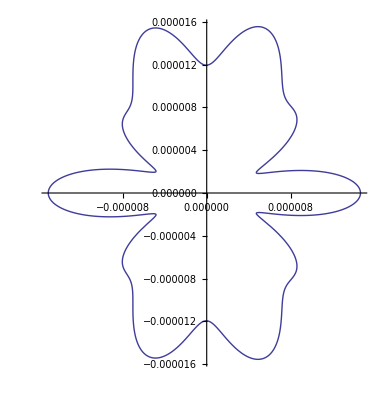

```mathematica
plot1=With[{lambda=1.},With[{r=50 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,phi=0,numberOfModes=5},PolarPlot[Abs[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes][[1]]],{theta,-Pi,Pi}]]]
```

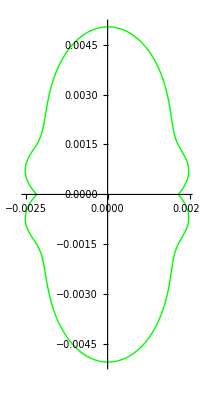

```mathematica
plot2=With[{lambda=1.},With[{r=50 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,phi=0,numberOfModes=5},PolarPlot[Abs[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes][[2]]],{theta,-Pi,Pi},PlotStyle->Green]]]
```

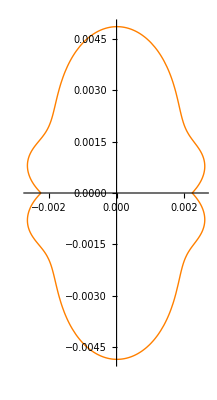

```mathematica
plot3=With[{lambda=1.},With[{r=50 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,phi=0,numberOfModes=5},PolarPlot[Abs[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes][[3]]],{theta,-Pi,Pi},PlotStyle->Orange]]]
```

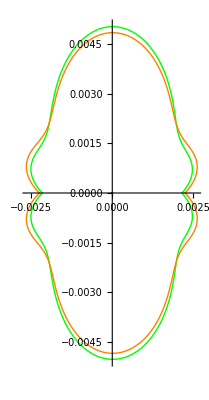

```mathematica
Show[plot1,plot2,plot3]
```

```mathematica
With[{lambda=1,n=2,m=1},With[{r=1 lambda,theta=10 Degree,phi=0,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].Pfunc[-m,n,theta,phi] Sin[theta]]]//N
```

0.000938116+0.000431076 ⅈ

```mathematica
With[{lambda=1,n=2,m=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},NIntegrate[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].Pfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"MultiDimensionalRule"]]]
```

0.00399448-0.00773028 ⅈ

```mathematica
ddata0=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Monitor[Table[NIntegrate[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].Pfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}],{n,m}]]]
```

{{0.155527+0.0247529 ⅈ,-0.110459-0.017424 ⅈ,0.0777635+0.0123764 ⅈ},{-0.0119834+0.0231908 ⅈ,0.0239668-0.046382 ⅈ,-0.0394921+0.0754041 ⅈ,0.00399447-0.00773033 ⅈ,-0.00049931+0.000966285 ⅈ},{-0.00156519-0.00225789 ⅈ,0.00575086+0.00829601 ⅈ,-0.0163667-0.0236108 ⅈ,0.0420374+0.0614219 ⅈ,-0.0013639-0.00196757 ⅈ,0.0000479238+0.0000691334 ⅈ,-2.17387×10^-6-3.13595×10^-6 ⅈ},{0.000215609+0.0000133791 ⅈ,-0.00121967-0.0000756836 ⅈ,0.00521552+0.000323634 ⅈ,-0.0196692-0.00122146 ⅈ,0.0700143+0.0040286 ⅈ,-0.00098346-0.0000610732 ⅈ,0.0000144876+8.98984×10^-7 ⅈ,-2.41998×10^-7-1.50166×10^-8 ⅈ,5.34744×10^-9+3.31823×10^-10 ⅈ},{-0.0000111721+8.38552×10^-6 ⅈ,0.000088323-0.0000662934 ⅈ,-0.000520448+0.000390637 ⅈ,0.0026559-0.00199346 ⅈ,-0.0125467+0.00941831 ⅈ,0.0567852-0.0429086 ⅈ,-0.000418223+0.000313944 ⅈ,3.16178×10^-6-2.37317×10^-6 ⅈ,-2.58159×10^-8+1.93769×10^-8 ⅈ,2.43394×10^-10-1.82687×10^-10 ⅈ,-3.07872×10^-12+2.31082×10^-12 ⅈ}}

```mathematica
ddata=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Monitor[Table[NIntegrate[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].Pfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"MultiDimensionalRule"],{n,1,numberOfModes},{m,-n,n}],{n,m}]]]
```

{{0.155527+0.0247529 ⅈ,-0.109974-0.0175029 ⅈ,0.0777635+0.0123764 ⅈ},{-0.0119834+0.0231908 ⅈ,0.0239669-0.0463817 ⅈ,-0.0391378+0.075741 ⅈ,0.00399448-0.00773028 ⅈ,-0.00049931+0.000966285 ⅈ},{-0.00156519-0.00225789 ⅈ,0.00575086+0.00829601 ⅈ,-0.0163672-0.0236109 ⅈ,0.0425233+0.0613428 ⅈ,-0.00136394-0.00196757 ⅈ,0.0000479238+0.0000691334 ⅈ,-2.17387×10^-6-3.13595×10^-6 ⅈ},{0.000215609+0.0000133791 ⅈ,-0.00121967-0.0000756836 ⅈ,0.00521552+0.000323637 ⅈ,-0.019669-0.00122051 ⅈ,0.0703698+0.00436663 ⅈ,-0.000983448-0.0000610255 ⅈ,0.0000144876+8.98991×10^-7 ⅈ,-2.41998×10^-7-1.50166×10^-8 ⅈ,5.34744×10^-9+3.31823×10^-10 ⅈ},{-0.0000111721+8.38552×10^-6 ⅈ,0.000088323-0.0000662934 ⅈ,-0.000520448+0.000390637 ⅈ,0.0026559-0.00199346 ⅈ,-0.012548+0.00941823 ⅈ,0.0572733-0.0429881 ⅈ,-0.000418265+0.000313941 ⅈ,3.16179×10^-6-2.37317×10^-6 ⅈ,-2.58159×10^-8+1.93769×10^-8 ⅈ,2.43394×10^-10-1.82687×10^-10 ⅈ,-3.07872×10^-12+2.31082×10^-12 ⅈ}}

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[Re[b2func[ddata,m,n,k,r]],{n,1,numberOfModes},{m,-n,n}]]],1*^-8]//MatrixForm
```

({1.,1.,1.}
{0.0625,0.25,1.,0.25,0.0625}
{0.00137174,0.0123457,0.111111,1.,0.111111,0.0123457,0.00137174}
{0.0000152588,0.000244141,0.00390625,0.0625,1.,0.0625,0.00390625,0.000244141,0.0000152588}
{1.024×10^-7,2.56×10^-6,0.000064,0.0016,0.04,1.,0.04,0.0016,0.000064,2.56×10^-6,1.024×10^-7})

```mathematica
N[bcoeff]//MatrixForm
```

({1.,1.,1.}
{0.0625,0.25,1.,0.25,0.0625}
{0.00137174,0.0123457,0.111111,1.,0.111111,0.0123457,0.00137174}
{0.0000152588,0.000244141,0.00390625,0.0625,1.,0.0625,0.00390625,0.000244141,0.0000152588}
{1.024×10^-7,2.56×10^-6,0.000064,0.0016,0.04,1.,0.04,0.0016,0.000064,2.56×10^-6,1.024×10^-7})

```mathematica
edata=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Monitor[Table[NIntegrate[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].BSinfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}],{n,m}]]];
```

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[Re[bfunc[edata,m,n,k,r]],{n,1,numberOfModes},{m,-n,n}]]],1*^-7]//MatrixForm
```

({0.998815,0.999999,0.998903}
{0.0625001,0.250449,1.,0.2486,0.0625001}
{0.00137176,0.0123446,0.115627,1.00001,0.11277,0.0123469,0.00137172}
{0.0000152586,0.000244277,0.00390398,0.0564084,1.00003,0.0690903,0.00390816,0.000244002,0.000015259}
{1.024×10^-7,2.55927×10^-6,0.0000642115,0.00160252,0.0477167,1.00004,0.0516984,0.00159767,0.000063997,2.56074×10^-6,1.024×10^-7})

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[bfunc[edata,m,n,k,r],{n,1,numberOfModes},{m,-n,n}]]],1*^-7]//MatrixForm
```

({0.998815-0.000369628 ⅈ,0.999999-2.25836×10^-7 ⅈ,0.998903+0.000459815 ⅈ}
{0.0625001+3.5483×10^-7 ⅈ,0.250449+0.00215392 ⅈ,1.-6.53825×10^-6 ⅈ,0.2486-0.0020005 ⅈ,0.0625001-3.74568×10^-7 ⅈ}
{0.00137176,0.0123446-7.71631×10^-7 ⅈ,0.115627-0.00268048 ⅈ,1.00001-8.35958×10^-6 ⅈ,0.11277-0.00474923 ⅈ,0.0123469+7.47204×10^-7 ⅈ,0.00137172}
{0.0000152586,0.000244277,0.00390398,0.0564084-0.000861935 ⅈ,1.00003+0.0000282087 ⅈ,0.0690903-0.00178584 ⅈ,0.00390816+1.29265×10^-6 ⅈ,0.000244002,0.000015259}
{1.024×10^-7,2.55927×10^-6,0.0000642115+1.0817×10^-7 ⅈ,0.00160252-4.4886×10^-6 ⅈ,0.0477167+0.00979989 ⅈ,1.00004+0.0000358776 ⅈ,0.0516984+0.00242698 ⅈ,0.00159767+5.15929×10^-6 ⅈ,0.000063997,2.56074×10^-6,1.024×10^-7})

```mathematica
gdata=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Monitor[Table[NIntegrate[Efieldsint[k,r,acoeff,bcoeff,theta,phi,numberOfModes].CSinfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}],{n,m}]]];
```

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[Re[afunc[gdata,m,n,k,r]],{n,1,numberOfModes},{m,-n,n}]]],1*^-6]//MatrixForm
```

({0.999109,0.999998,0.999041}
{0.250006,0.500035,1.,0.498284,0.250007}
{0.037037,0.111112,0.335893,1.00001,0.33504,0.111112,0.037037}
{0.00390625,0.0156249,0.0625,0.244409,1.00003,0.255564,0.0625002,0.0156249,0.00390625}
{0.00032,0.0016,0.00799988,0.0400018,0.203259,1.00005,0.205234,0.0400005,0.008,0.0016,0.00032})

```mathematica
N[acoeff]//MatrixForm
```

({1.,1.,1.}
{0.25,0.5,1.,0.5,0.25}
{0.037037,0.111111,0.333333,1.,0.333333,0.111111,0.037037}
{0.00390625,0.015625,0.0625,0.25,1.,0.25,0.0625,0.015625,0.00390625}
{0.00032,0.0016,0.008,0.04,0.2,1.,0.2,0.04,0.008,0.0016,0.00032})

## Definiciones del campo de un dipolo (Balanis, ec. (4.10a), (4.10b))

```mathematica
Edipoler[r_,theta_,k_,eta_,l_,I0_]:=eta I0 l Cos[theta]/(2 Pi r^2) (1+1/(I k r)) Exp[-I k r]
```

```mathematica
Edipoletheta[r_,theta_,k_,eta_,l_,I0_]:=I eta k I0 l Sin[theta]/(4 Pi r) (1+1/(I k r)-1/(k r)^2) Exp[-I k r]
```

```mathematica
Edipolefarfieldtheta[r_,theta_,k_,eta_,l_,I0_]:=I eta k I0 l Sin[theta]/(4 Pi r) Exp[-I k r]
```

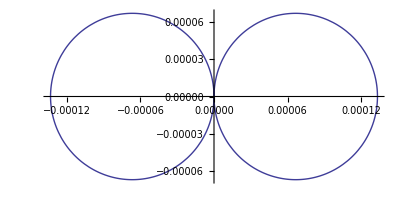

```mathematica
With[{lambda=1},With[{r=150 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[Abs[Edipoler[r,theta,k,eta,l,I0]],{theta,-Pi,Pi}]]]
```

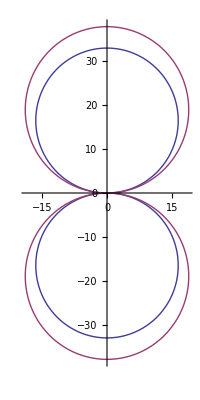

```mathematica
With[{lambda=1},With[{r=0.25 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[{Abs[Edipoletheta[r,theta,k,eta,l,I0]],Abs[Edipolefarfieldtheta[r,theta,k,eta,l,I0]]},{theta,-Pi,Pi}]]]
```

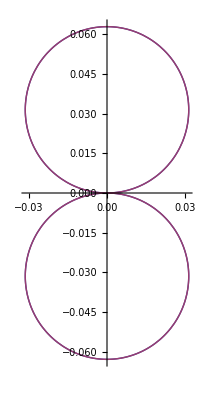

```mathematica
With[{lambda=1},With[{r=150 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[{Abs[Edipoletheta[r,theta,k,eta,l,I0]],Abs[Edipolefarfieldtheta[r,theta,k,eta,l,I0]]},{theta,-Pi,Pi}]]]
```

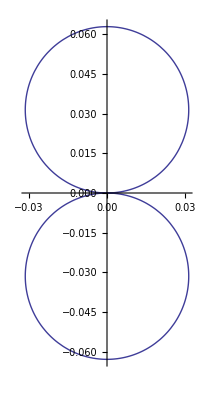

```mathematica
With[{lambda=1},With[{r=150 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},PolarPlot[Abs[Edipolefarfieldtheta[r,theta,k,eta,l,I0]],{theta,-Pi,Pi}]]]
```

```mathematica
numberOfModes=20
```

20

```mathematica
phiArray={0}
```

{0}

```mathematica
thetaArray=Table[theta Degree,{theta,-60,60,1}];
```

```mathematica
deltaPhi=1 Degree
```

°

```mathematica
deltaTheta=1 Degree
```

°

```mathematica
EpthetaArray=With[{lambda=1},With[{r=10 lambda,k=2 Pi/lambda,eta=120 Pi,I0=1,l=0.05 lambda},Edipoletheta[r,thetaArray,k,eta,l,I0]]];
```

```mathematica
Length[thetaArray]
```

121

```mathematica
EpphiArray=Table[0,{Length[thetaArray]}];
```

```mathematica
With[{lambda=1,n=1,m=0},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},NIntegrate[{Edipoler[r,theta,k,eta,l,I0],Edipoletheta[r,theta,k,eta,l,I0],0}.Pfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"]]]
```

5.01442-0.79807 ⅈ

```mathematica
With[{lambda=1,n=1,m=0},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},NIntegrate[{Edipoler[r,theta,k,eta,l,I0],Edipoletheta[r,theta,k,eta,l,I0],0}.Bfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"]]]
```

-5.02655-30.7828 ⅈ

```mathematica
ddatadipole=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Monitor[Table[NIntegrate[{Edipoler[r,theta,k,eta,l,I0],Edipoletheta[r,theta,k,eta,l,I0],0}.Pfunc[-m,n,theta,phi] Sin[theta],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}],{n,m}]]];
```

```mathematica
edatadipole=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[NIntegrate[{Edipoler[r,theta,k,eta,l,I0],Edipoletheta[r,theta,k,eta,l,I0],0}.BSinfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}]]];
```

```mathematica
gdatadipole=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[NIntegrate[{Edipoler[r,theta,k,eta,l,I0],Edipoletheta[r,theta,k,eta,l,I0],0}.CSinfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi},Method->"Trapezoidal"],{n,1,numberOfModes},{m,-n,n}]]];
```

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[bfunc[edatadipole,m,n,k,r],{n,1,numberOfModes},{m,-n,n}]]],1*^-8]//MatrixForm
```

({0,43.3325-14.5393 ⅈ,0}
{0,0,0,0,0}
{0,0,0,-0.000220001+0.000507317 ⅈ,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,-0.00200901-0.000572887 ⅈ,0,0,0,0,0})

```mathematica
Chop[edatadipole]//MatrixForm
```

({0,-5.02655-30.7828 ⅈ,0}
{0,0,0,0,0}
{0,0,0,-0.0000353043-0.000216205 ⅈ,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,-0.0000891836-0.000546163 ⅈ,0,0,0,0,0})

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[b2func[ddatadipole,m,n,k,r],{n,1,numberOfModes},{m,-n,n}]]],1*^-8]//MatrixForm
```

({0,-43.3435+14.1552 ⅈ,0}
{0,0,0,0,0}
{0,0,0,-0.0714746+0.1486 ⅈ,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,-0.152632-0.0806374 ⅈ,0,0,0,0,0})

```mathematica
Chop[ddatadipole]//MatrixForm
```

({0,5.01442-0.79807 ⅈ,0}
{0,0,0,0,0}
{0,0,0,-0.0121549+0.00193451 ⅈ,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,-0.0122082+0.00194299 ⅈ,0,0,0,0,0})

```mathematica
Chop[With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=5},Table[afunc[gdatadipole,m,n,k,r],{n,1,numberOfModes},{m,-n,n}]]],1*^-8]//MatrixForm
```

({0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0})

```mathematica
Chop[gdatadipole]//MatrixForm
```

({0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0})

```mathematica
With[{lambda=1.},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,theta=0,phi=0,numberOfModes=1},ac[k,r,theta,phi,edata,gdata,numberOfModes]]]
```

{{{0.+0. ⅈ,Indeterminate,Indeterminate},{3/2 ((0.+0. ⅈ)-(0.000104703+0.0259715 ⅈ) {{0.},{-1.80534×10^-16-1.42958×10^-16 ⅈ,-5.02655-30.7827 ⅈ,-3.71878×10^-16+1.25371×10^-16 ⅈ},{1.79978×10^-15+1.34896×10^-15 ⅈ,-4.57283×10^-16-1.67574×10^-15 ⅈ,3.87629×10^-16+6.7806×10^-16 ⅈ,4.58766×10^-16-4.23347×10^-18 ⅈ,1.74152×10^-16-1.82037×10^-17 ⅈ},{1.61871×10^-15-9.02056×10^-16 ⅈ,3.63723×10^-15+8.04933×10^-15 ⅈ,-7.71735×10^-16-3.57537×10^-15 ⅈ,-4.25387×10^-16+6.31006×10^-17 ⅈ,1.94208×10^-16-1.00966×10^-16 ⅈ,4.97249×10^-17-6.67682×10^-17 ⅈ,-6.29007×10^-18-1.01771×10^-17 ⅈ},{-6.37932×10^-14+4.25463×10^-15 ⅈ,5.47715×10^-14-7.28567×10^-14 ⅈ,2.99327×10^-15+2.67885×10^-15 ⅈ,-7.80992×10^-17-4.63974×10^-15 ⅈ,9.28944×10^-16+3.52756×10^-15 ⅈ,-1.3553×10^-16+4.26848×10^-17 ⅈ,-4.98733×10^-18-2.29377×10^-17 ⅈ,1.54217×10^-17+9.59234×10^-18 ⅈ,-1.70474×10^-18+2.29476×10^-19 ⅈ},{3.47014×10^-14-1.22014×10^-13 ⅈ,2.3664×10^-12+1.37406×10^-11 ⅈ,3.54716×10^-14-8.88178×10^-14 ⅈ,4.21885×10^-15-2.57849×10^-14 ⅈ,-1.10096×10^-14-1.48428×10^-15 ⅈ,5.00685×10^-16+2.74824×10^-15 ⅈ,1.37156×10^-16-1.67158×10^-17 ⅈ,-2.37186×10^-17-4.70002×10^-17 ⅈ,-2.92164×10^-18-2.36873×10^-18 ⅈ,5.78511×10^-18+4.63699×10^-17 ⅈ,6.14035×10^-20-1.67592×10^-19 ⅈ}}[0,1]),Indeterminate,Indeterminate},{0.+0. ⅈ,Indeterminate,Indeterminate}}}

```mathematica
wthetaData=With[{lambda=1},With[{k=2 Pi/lambda,eta=120 Pi},wfunc[k,eta,EpthetaArray]]];
```

```mathematica
wphiData=With[{lambda=1},With[{k=2 Pi/lambda,eta=120 Pi},wfunc[k,eta,EpphiArray]]];
```

```mathematica
N[With[{lambda=1},With[{r=100 lambda,thetas=30 Degree,phis=20 Degree,k=2 Pi/lambda,eta=120 Pi,numberOfModes=20},Efarfield[r,thetas,phis,k,eta,EpthetaArray,EpphiArray,thetaArray,phiArray,deltaTheta,deltaPhi,numberOfModes]]]]
```

{-5.62588×10^-20-8.35942×10^-21 ⅈ,6.56643×10^-21+2.58456×10^-20 ⅈ,1.06398×10^-20+5.55523×10^-20 ⅈ}

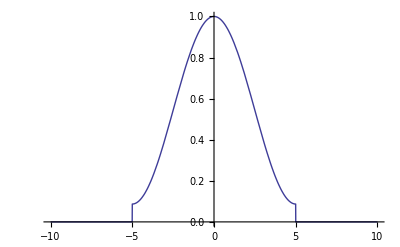

```mathematica
Plot[HammingWindow[x/10],{x,-10,10}]
```

```mathematica
intensityModes=Table[HammingWindow[m/10],{m,-5,5}];
```

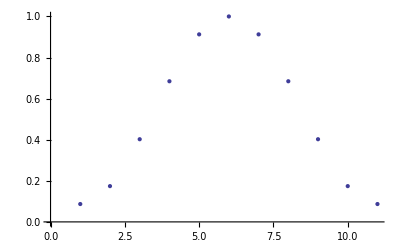

```mathematica
ListPlot[intensityModes]
```

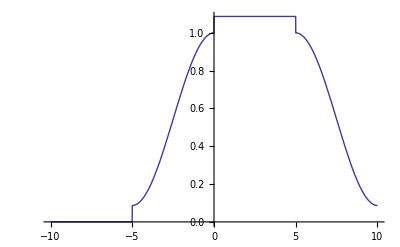

```mathematica
Plot[HammingWindow[x/10]+HammingWindow[(x-5)/10],{x,-10,10}]
```

```mathematica
intensityModes2=Table[HammingWindow[m/10]+HammingWindow[(m-5)/10],{m,-5,10}];N[intensityModes2]
```

{0.0869565,0.174144,0.402405,0.684551,0.912812,1.08696,1.08696,1.08696,1.08696,1.08696,1.08696,0.912812,0.684551,0.402405,0.174144,0.0869565}

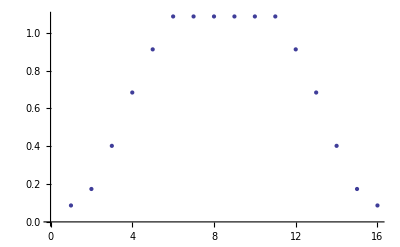

```mathematica
ListPlot[intensityModes2]
```

```mathematica
Grid[ArrayReshape[Join[{{"w (cm^-1)","frequency (Hz)"}},Flatten[Table[i+10 j,{i,3},{j,2}],1]],{3,2}],Frame->All]
```

w (cm^-1) | frequency (Hz)
11 | 21
12 | 22

```mathematica
With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,m=-1,n=1},Plot3D[Re[{Edipoletheta[r,theta,k,eta,l,I0],0}.Cfunc[m,n,theta,phi]],{theta,0,Pi},{phi,0,2 Pi}]]]
```

-Graphics3D-

```mathematica
edata=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=1},Table[NIntegrate[{Edipoletheta[r,theta,k,eta,l,I0],0}.Bfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi}],{n,1,numberOfModes},{m,-n,n}]]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.80534×10^-16 - 1.42958×10^-16\ ⅈ and 5.34529×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.71878×10^-16 + 1.25371×10^-16\ ⅈ and 2.67101×10^-13 for the integral and error estimates.

```mathematica
gdata=With[{lambda=1},With[{r=1 lambda,I0=1,l=lambda/50, k=2 Pi/lambda,eta=120 Pi,numberOfModes=1},Table[NIntegrate[{Edipoletheta[r,theta,k,eta,l,I0],0}.Cfunc[-m,n,theta,phi],{phi,0,2 Pi},{theta,0,Pi}],{n,1,numberOfModes},{m,-n,n}]]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.42594×10^-15 + 2.21004×10^-15\ ⅈ and 4.60762×10^-15 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.33899×10^-15 - 5.06539×10^-16\ ⅈ and 2.34996×10^-15 for the integral and error estimates.

```mathematica
edata
```

{{-1.80534×10^-16-1.42958×10^-16 ⅈ,-5.02655-30.7827 ⅈ,-3.71878×10^-16+1.25371×10^-16 ⅈ}}

```mathematica
gdata
```

{{-1.42594×10^-15+2.21004×10^-15 ⅈ,0.,-1.33899×10^-15-5.06539×10^-16 ⅈ}}

```mathematica
gdata
```

{{{-1.34929×10^-16-2.52619×10^-17 ⅈ,-5.46675×10^-18+1.28543×10^-17 ⅈ},{0.,0.0502655+3.15747 ⅈ},{-1.6507×10^-16+6.63532×10^-17 ⅈ,4.07528×10^-17-2.61494×10^-17 ⅈ}}}